# MOT calbration

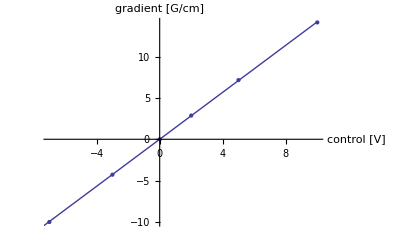

G/cm/ControlV

1.42316

gradent in G/cm for 9V control voltage

-12.8085

```mathematica
mv={10, 0, 5,-3,-7, 2}; (*control voltage in V*)
mh={101.292, 0.057, 51.305,-30.72,-71.739, 20.565};(*hall probe voltage in mV*)
mA=mh/34.2857; (*current in Amps*)
gradB=4.79mA;(*B field gradient in G/cm*)
MOT=Thread[{mv,gradB}];
fitfn=a x;
fit=FindFit[MOT,fitfn,{a},x];
Show[{ListPlot[MOT,AxesLabel->{"control [V]","gradient [G/cm]"}],Plot[fitfn/.fit,{x,-10,10}]}]

Print["G/cm/ControlV"]
a/.fit
Print["gradent in G/cm for 9V control voltage"]
fitfn/.fit/.x->-9
```

# x shim calibration

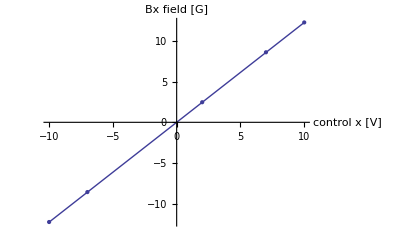

G/ControlV

1.22527

B field in G for -0.07 V control voltage (exp params)

-0.0857686

B field in G for 0.13 V control voltage (zero the field)

0.159284

```mathematica
xv={10,-7,-10, 2, 7}; (*control voltage in V*)
xh={35.058,-24.487,-34.995, 7.045, 24.583};(*hall probe voltage in mV*)
xA=xh/34.2857; (*current in Amps*)
xB=11.99xA;(*B field in G*)
xShim=Thread[{xv,xB}];
fitfn=a x;
fit=FindFit[xShim,fitfn,{a},x];
Show[{ListPlot[xShim,AxesLabel->{"control x [V]","Bx field [G]"}],Plot[fitfn/.fit,{x,-10,10}]}]

Print["G/ControlV"]
a/.fit
Print["B field in G for -0.07 V control voltage (exp params)"]
fitfn/.fit/.x->-.07

Print["B field in G for 0.13 V control voltage (zero the field)"]
fitfn/.fit/.x->.13
```

# y shim calibration

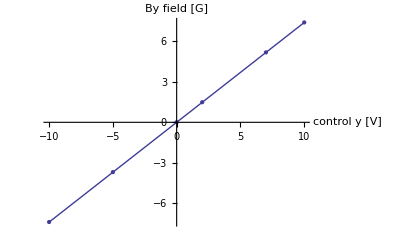

G/ControlV

0.738455

B field in G for -0.8 V control voltage (exp params)

-0.590764

B field in G for -.49 V control voltage (zero the field)

-0.361843

```mathematica
yv={0,10,-10, 2,-5, 7}; (*control voltage in V*)
yh={0.044, 35.287,-35.225, 7.096,-17.593, 24.717};(*hall probe voltage in mV*)
yA=yh/34.2857; (*current in Amps*)
yB=7.18yA;(*B field in G*)
yShim=Thread[{yv,yB}];
fitfn=a x;
fit=FindFit[yShim,fitfn,{a},x];
Show[{ListPlot[yShim,AxesLabel->{"control y [V]","By field [G]"}],Plot[fitfn/.fit,{x,-10,10}]}]

Print["G/ControlV"]
a/.fit
Print["B field in G for -0.8 V control voltage (exp params)"]
fitfn/.fit/.x->-.8

Print["B field in G for -.49 V control voltage (zero the field)"]
fitfn/.fit/.x->-.49
```

# z shim calibration

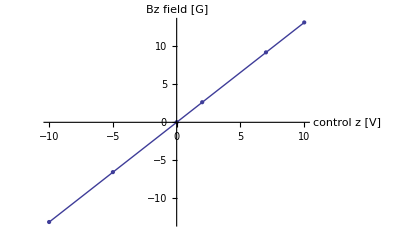

G/ControlV

1.3155

B field in G for 1.35 V control voltage (exp params)

1.77592

B field in G for 0.26 V control voltage (zero the field)

0.342029

```mathematica
zv={0,10,-10, 2,-5, 7}; (*control voltage in V*)
zh={0.045, 35.291,-35.224, 7.098,-17.595, 24.717};(*hall probe voltage in mV*)
zA=zh/34.2857; (*current in Amps*)
zB=12.79zA;(*B field in G*)
zShim=Thread[{zv,zB}];
fitfn=a x;
fit=FindFit[zShim,fitfn,{a},x];
Show[{ListPlot[zShim,AxesLabel->{"control z [V]","Bz field [G]"}],Plot[fitfn/.fit,{x,-10,10}]}]

Print["G/ControlV"]
a/.fit
Print["B field in G for 1.35 V control voltage (exp params)"]
fitfn/.fit/.x->1.35

Print["B field in G for 0.26 V control voltage (zero the field)"]
fitfn/.fit/.x->.26
```